```mathematica
RadioButtonBar[
Dynamic[fileName],
{
"~/Downloads/optimizerHistory.json",
"/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json"
},Appearance->"Vertical"]

raw=Import[fileName];
```

| ~/Downloads/optimizerHistory.json
 | /Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json

```mathematica
raw= Association[#]&/@raw;
raw=Select[raw,NumericQ[#["maximizeMe"]]&];
```

```mathematica
(*Optional: Drop rows with non-numeric values*)
Length[raw]
raw = Select[raw,AllTrue[Values[#],NumericQ]&];
Length[raw]
```

758

756

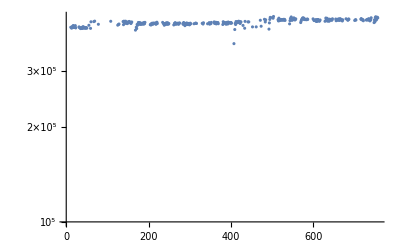

```mathematica
ListLogPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->{1*^5,All},
Joined->False
]
```

```mathematica
ListLogPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->{4*^5,All},
Joined->False
]
```

```mathematica
bestCase = MaximalBy[raw,#["maximizeMe"]&][[1]]
```

<|L1PhaseSet→-21.5106,L2PhaseSet→-38.4544,S1EL_xOffset→0.00324531,S1EL_yOffset→0.000700899,S2EL_xOffset→-0.000149532,S2EL_yOffset→0.000203807,S2ER_xOffset→-0.000172875,S2ER_yOffset→0.00112827,S1ER_xOffset→0.00396142,S1ER_yOffset→0.00155118,Q5FFkG→-88.216,Q4FFkG→-75.6636,Q3FFkG→100.702,Q2FFkG→118.142,Q1FFkG→-231.534,Q0FFkG→141.126,XC1FFkG→0.354358,XC3FFkG→-0.187733,YC1FFkG→0.00778248,YC2FFkG→-0.0178957,PDrive_mean_x→4.9229×10^-6,PDrive_mean_y→-6.1001×10^-6,PDrive_sigma_x→0.0000380709,PDrive_sigma_y→0.0000237847,PDrive_mean_xp→0.00067433,PDrive_mean_yp→0.000108456,PDrive_median_x→1.4295×10^-6,PDrive_median_y→-4.7843×10^-6,PDrive_median_xp→0.000709291,PDrive_median_yp→0.000101378,PDrive_sigmaSI90_x→0.0000271289,PDrive_sigmaSI90_y→0.0000226482,PDrive_emitSI90_x→0.000060426,PDrive_emitSI90_y→0.000017811,PDrive_zLen→0.0000205347,PDrive_zCentroid→991.332,PWitness_mean_x→-3.437×10^-6,PWitness_mean_y→-2.6851×10^-6,PWitness_sigma_x→0.0000152584,PWitness_sigma_y→0.0000211111,PWitness_mean_xp→0.000513041,PWitness_mean_yp→0.0000552864,PWitness_median_x→-4.365×10^-6,PWitness_median_y→-6.028×10^-7,PWitness_median_xp→0.00051628,PWitness_median_yp→0.0000562385,PWitness_sigmaSI90_x→0.0000140727,PWitness_sigmaSI90_y→0.0000176546,PWitness_emitSI90_x→7.9497×10^-6,PWitness_emitSI90_y→3.5439×10^-6,PWitness_zLen→0.0000205402,PWitness_zCentroid→991.332,bunchSpacing→0.000105491,transverseCentroidOffset→9.0305×10^-6,lostChargeFraction→0.,maximizeMe→445635.|>

```mathematica
(*Format for yml*)
string = ""
Do[
string = string<>key<>" : "<>ToString[bestCase[key],CForm]<>"\n",
{key,Keys[bestCase]}
]
string
```

L1PhaseSet : -21.5106480909
L2PhaseSet : -38.4543899528
S1EL_xOffset : 0.0032453071
S1EL_yOffset : 0.0007008989
S2EL_xOffset : -0.0001495318
S2EL_yOffset : 0.0002038073
S2ER_xOffset : -0.0001728747
S2ER_yOffset : 0.0011282717
S1ER_xOffset : 0.0039614217
S1ER_yOffset : 0.0015511828
Q5FFkG : -88.2160004994
Q4FFkG : -75.6636086433
Q3FFkG : 100.7024909818
Q2FFkG : 118.1415881081
Q1FFkG : -231.5339756568
Q0FFkG : 141.1258294017
XC1FFkG : 0.3543579125
XC3FFkG : -0.1877331377
YC1FFkG : 0.0077824836
YC2FFkG : -0.0178956999
PDrive_mean_x : 4.9229e-6
PDrive_mean_y : -6.1001e-6
PDrive_sigma_x : 0.0000380709
PDrive_sigma_y : 0.0000237847
PDrive_mean_xp : 0.0006743296
PDrive_mean_yp : 0.0001084562
PDrive_median_x : 1.4295e-6
PDrive_median_y : -4.7843e-6
PDrive_median_xp : 0.0007092907
PDrive_median_yp : 0.0001013784
PDrive_sigmaSI90_x : 0.0000271289
PDrive_sigmaSI90_y : 0.0000226482
PDrive_emitSI90_x : 0.000060426
PDrive_emitSI90_y : 0.000017811
PDrive_zLen : 0.0000205347
PDrive_zCentroid : 991.3317341924
PWitness_mean_x : -3.437e-6
PWitness_mean_y : -2.6851e-6
PWitness_sigma_x : 0.0000152584
PWitness_sigma_y : 0.0000211111
PWitness_mean_xp : 0.0005130412
PWitness_mean_yp : 0.0000552864
PWitness_median_x : -4.365e-6
PWitness_median_y : -6.028e-7
PWitness_median_xp : 0.0005162797
PWitness_median_yp : 0.0000562385
PWitness_sigmaSI90_x : 0.0000140727
PWitness_sigmaSI90_y : 0.0000176546
PWitness_emitSI90_x : 7.9497e-6
PWitness_emitSI90_y : 3.5439e-6
PWitness_zLen : 0.0000205402
PWitness_zCentroid : 991.331839683
bunchSpacing : 0.0001054905
transverseCentroidOffset : 9.0305e-6
lostChargeFraction : 0.
maximizeMe : 445634.6319404938

```mathematica
Norm[{bestCase["PDrive_mean_x"],bestCase["PDrive_mean_y"]}-{bestCase["PWitness_mean_x"],bestCase["PWitness_mean_y"]}]
```

9.03051×10^-6

## Plot all

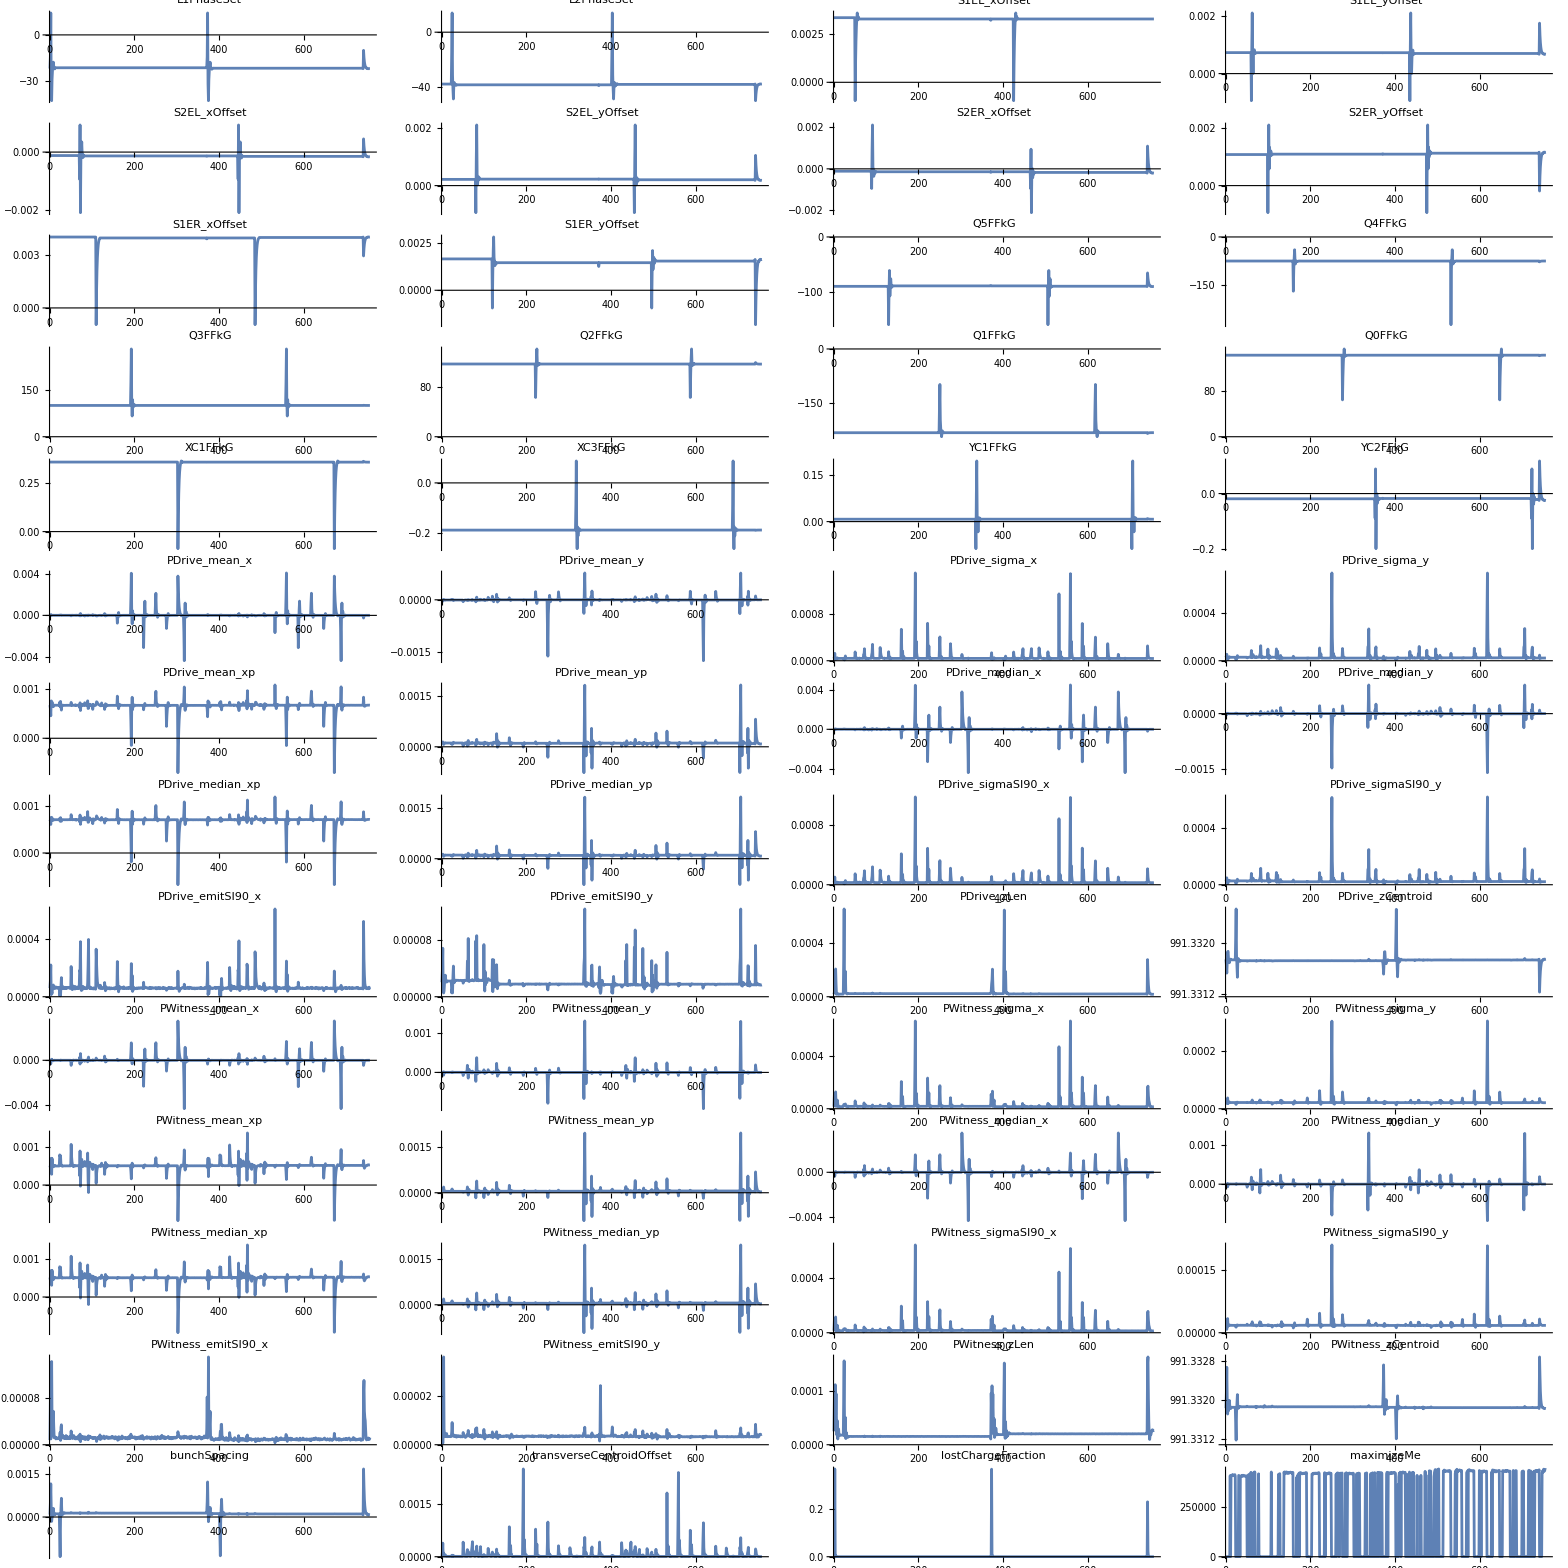

```mathematica
imgArr=Table[
ListPlot[
raw[[All,key]],
PlotLabel->key,
ImageSize->400,
LabelStyle->15,
PlotRange->All,
Joined->True
],
{key,Keys[raw[[1]]]}
];

displayCols = 4;
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
]//TableForm
```

## Dump for symbolic regression

Open the CSV in excel, do the automatic suggestion, and resave

```mathematica
Export[
"~/srData.csv",
Dataset[raw]
]
```

~/srData.csv

## Linear model fit

```mathematica
freeVars=Intersection[
Keys[raw[[1]]],
{"L1PhaseSet","L2PhaseSet","Q1EkG","Q2EkG","Q3EkG","Q4EkG","Q5EkG","Q6EkG","S1ELkG","S2ELkG","S3ELkG","S3ERkG","S2ERkG","S1ERkG","S1EL_xOffset","S1EL_yOffset","S2EL_xOffset","S2EL_yOffset","S2ER_xOffset","S2ER_yOffset","S1ER_xOffset","S1ER_yOffset","Q5FFkG","Q4FFkG","Q3FFkG","Q2FFkG","Q1FFkG","Q0FFkG", "XC1FFkG","XC3FFkG","YC1FFkG","YC2FFkG"}
]
(*Mathematica doesn't like underscores...*)
freeVarsMathematica=StringReplace[#,"_"->""]&/@freeVars;
```

{L1PhaseSet,L2PhaseSet,Q0FFkG,Q1FFkG,Q2FFkG,Q3FFkG,Q4FFkG,Q5FFkG,S1EL_xOffset,S1EL_yOffset,S1ER_xOffset,S1ER_yOffset,S2EL_xOffset,S2EL_yOffset,S2ER_xOffset,S2ER_yOffset,XC1FFkG,XC3FFkG,YC1FFkG,YC2FFkG}

```mathematica
fitVar = "PDrive_zLen"
```

PDrive_zLen

```mathematica
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVarsMathematica,
Symbol[#]&/@freeVarsMathematica
]
```

FittedModel[…]

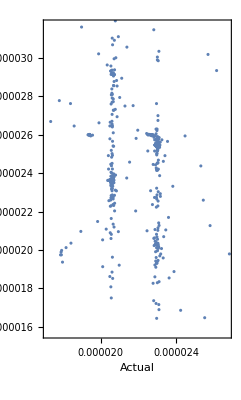

```mathematica
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
AspectRatio->Automatic,
Frame->True,
FrameLabel->{"Actual","Predicted"}
]
```

```mathematica
Minimize[
lm["BestFit"],
Symbol[#]&/@freeVarsMathematica
]
```

NMinimize::ubnd: The problem is unbounded.

{-∞,{L1PhaseSet→Indeterminate,L2PhaseSet→Indeterminate,Q0FFkG→Indeterminate,Q1FFkG→Indeterminate,Q2FFkG→Indeterminate,Q3FFkG→Indeterminate,Q4FFkG→Indeterminate,Q5FFkG→Indeterminate,S1ELxOffset→Indeterminate,S1ELyOffset→Indeterminate,S1ERxOffset→Indeterminate,S1ERyOffset→Indeterminate,S2ELxOffset→Indeterminate,S2ELyOffset→Indeterminate,S2ERxOffset→Indeterminate,S2ERyOffset→Indeterminate,XC1FFkG→Indeterminate,XC3FFkG→Indeterminate,YC1FFkG→Indeterminate,YC2FFkG→Indeterminate}}

*facepalm* It’s a linear model, obviously it’s unbounded

```mathematica
lm["ANOVATable"]
```

| DF | SS | MS | F-Statistic | P-Value
L1PhaseSet | 1 | 7.09349×10^-10 | 7.09349×10^-10 | 1.45979 | 0.227352
L2PhaseSet | 1 | 6.7717×10^-7 | 6.7717×10^-7 | 1393.57 | 7.05974×10^-172
Q0FFkG | 1 | 6.22397×10^-12 | 6.22397×10^-12 | 0.0128085 | 0.909923
Q1FFkG | 1 | 1.79366×10^-10 | 1.79366×10^-10 | 0.369123 | 0.54367
Q2FFkG | 1 | 3.30346×10^-10 | 3.30346×10^-10 | 0.679828 | 0.409913
Q3FFkG | 1 | 2.92989×10^-11 | 2.92989×10^-11 | 0.060295 | 0.806099
Q4FFkG | 1 | 2.44501×10^-13 | 2.44501×10^-13 | 0.000503165 | 0.98211
Q5FFkG | 1 | 1.2951×10^-8 | 1.2951×10^-8 | 26.6521 | 3.13853×10^-7
S1ELxOffset | 1 | 1.05669×10^-10 | 1.05669×10^-10 | 0.217458 | 0.641122
S1ELyOffset | 1 | 2.63155×10^-8 | 2.63155×10^-8 | 54.1554 | 4.96735×10^-13
S1ERxOffset | 1 | 2.03157×10^-9 | 2.03157×10^-9 | 4.18084 | 0.0412393
S1ERyOffset | 1 | 5.85735×10^-8 | 5.85735×10^-8 | 120.54 | 4.49715×10^-26
S2ELxOffset | 1 | 3.05684×10^-9 | 3.05684×10^-9 | 6.29076 | 0.0123513
S2ELyOffset | 1 | 4.5615×10^-9 | 4.5615×10^-9 | 9.38724 | 0.00226485
S2ERxOffset | 1 | 1.20614×10^-8 | 1.20614×10^-8 | 24.8216 | 7.8468×10^-7
S2ERyOffset | 1 | 8.59004×10^-9 | 8.59004×10^-9 | 17.6777 | 0.0000293942
XC1FFkG | 1 | 5.74551×10^-11 | 5.74551×10^-11 | 0.118238 | 0.731051
XC3FFkG | 1 | 1.84003×10^-11 | 1.84003×10^-11 | 0.0378665 | 0.845765
YC1FFkG | 1 | 5.3944×10^-13 | 5.3944×10^-13 | 0.00111013 | 0.97343
YC2FFkG | 1 | 6.97064×10^-9 | 6.97064×10^-9 | 14.3451 | 0.000164611
Error | 735 | 3.57155×10^-7 | 4.85925×10^-10 |  | 
Total | 755 | 1.17087×10^-6 |  |  |

### Fit all dependent vars

```mathematica
allFitVars  = Complement[
Keys[raw[[1]]],
freeVars
];
```

```mathematica
imgArr=Table[
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVarsMathematica,
Symbol[#]&/@freeVarsMathematica
];

Show[
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
Frame->True,
FrameLabel->{"Actual","Predicted"},
PlotLabel->Row[{fitVar,": ",Style[ToString[lm["RSquared"]],ColorData["Rainbow"][lm["RSquared"]]]}],
ImageSize->400,
AspectRatio->1,
LabelStyle->15,
PlotRange->All
],
Plot[x,{x,Min[lm["Response"]],Max[lm["Response"]]},PlotStyle->Red]
],
{fitVar,allFitVars}
];
```

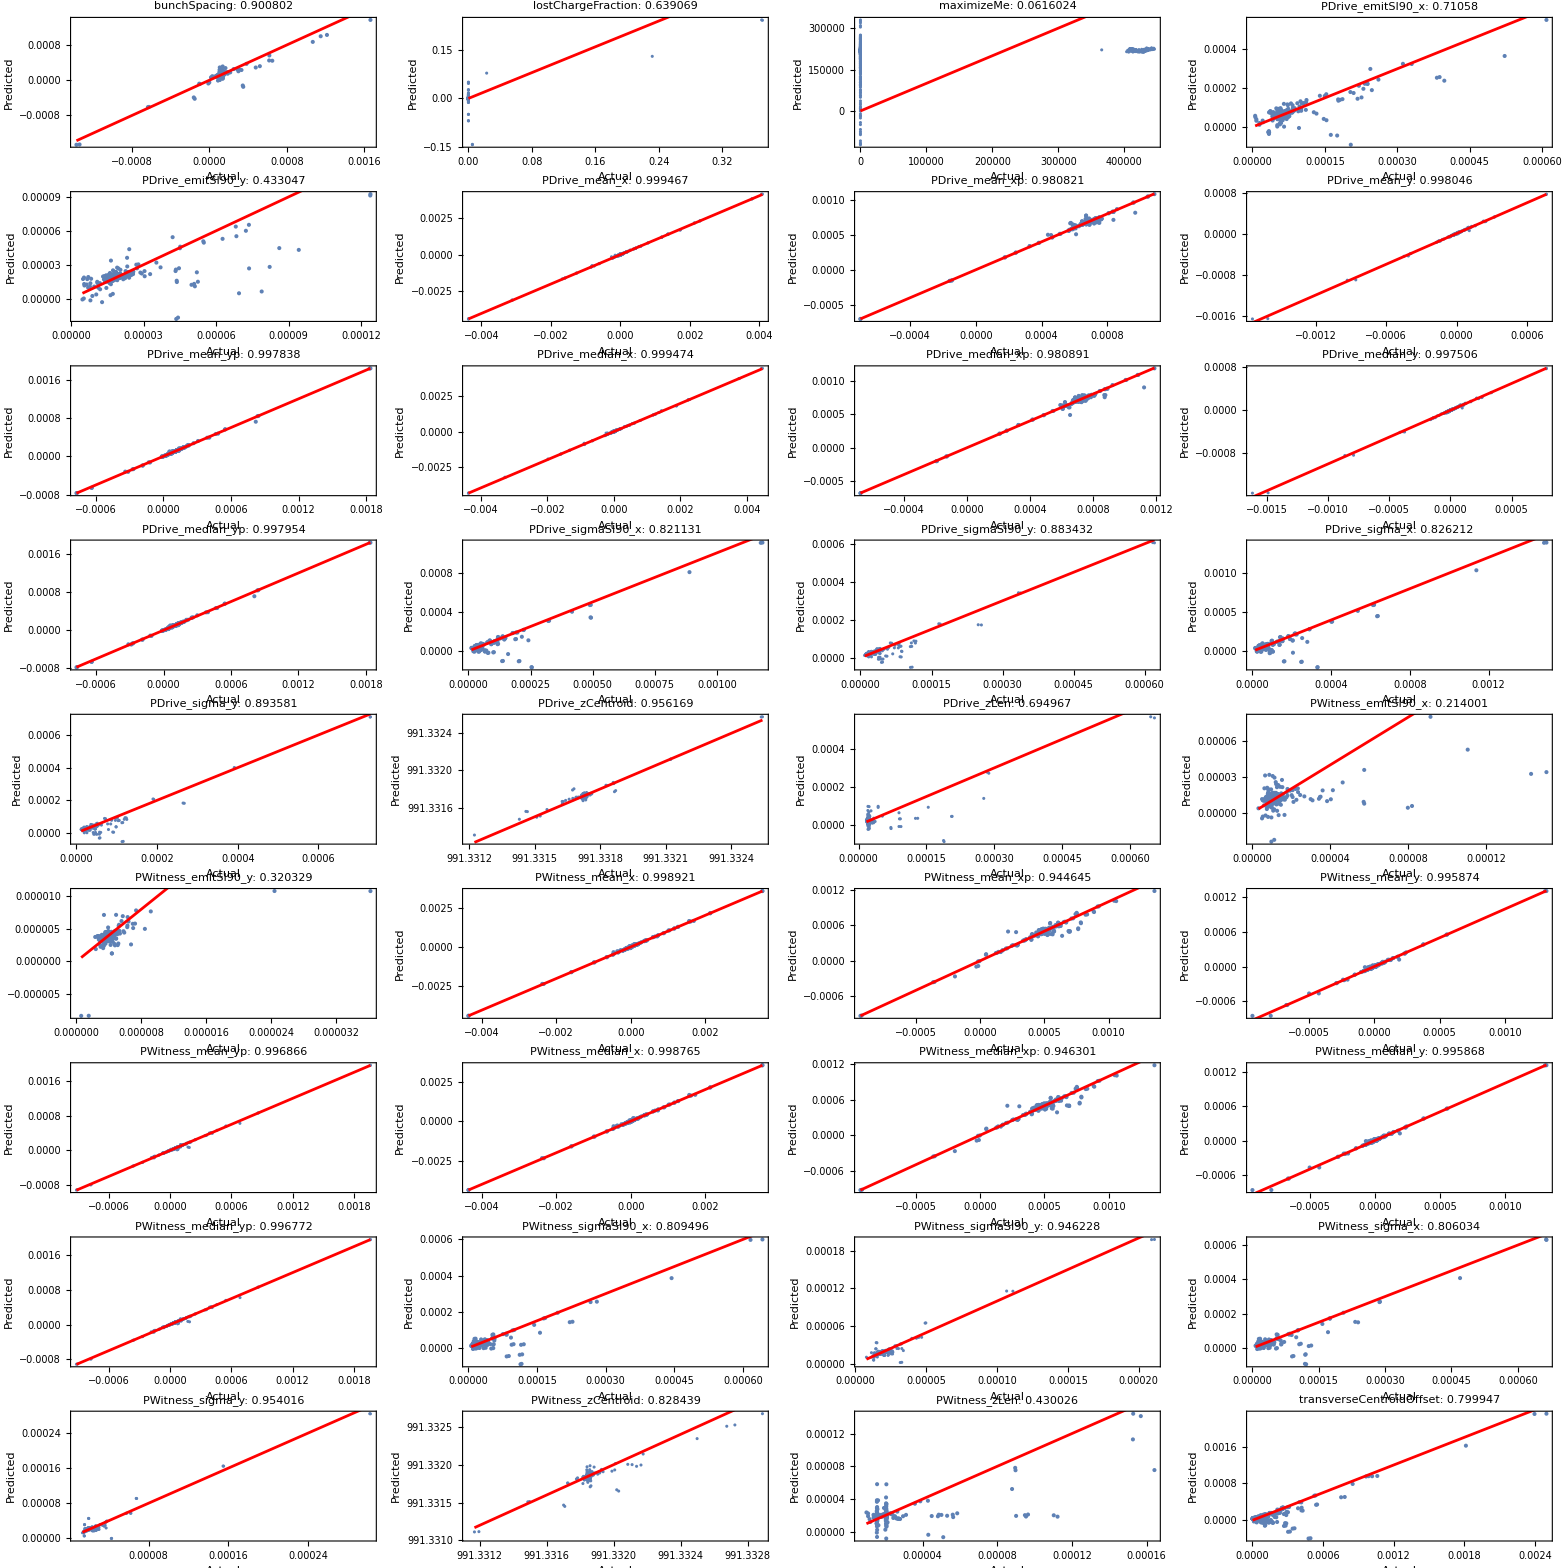

```mathematica
displayCols = 4;
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
]//TableForm
```